# Coherence simulation, with proper sampling and a general transfer function

```mathematica
$Assumptions = A > 0 &&ϕ>=0 && θ >= 0 && f >= 0 && f <= 1 && θ < 2 * π && ϕ < 2 * π && Y > 0 && B > 0 && P > 0&&H>0 && J>0 && T>=0 ;
```

Following Timmer & König, define the spectrum of the reference time series 

Where  are random variables drawn:

```mathematica
F1 = Sqrt[P/2] * (A + ⅈ B);
G[x_]:=1/Sqrt[2π] Exp[-x^2/2];
```

Then define the spectrum of the second time series


Where, similarly


and T is a general transfer function

```mathematica
F2 = T F1 *ⅇ^(ⅈ*ϕ) + Sqrt[P/2] * (H + ⅈ J);
```

Define the cross spectrum:

```mathematica
CC = Conjugate[F1] * F2 //FullSimplify
```

1/2 (A-ⅈ B) P (H+ⅈ J+(A+ⅈ B) ⅇ^(ⅈ ϕ) T)

Average and square the cross spectrum

```mathematica
CCav = Integrate[
Integrate[
Integrate[
Integrate[
CC * G[A] * G[B] * G[H] * G[J],{A,-Infinity,Infinity}],
{B,-Infinity,Infinity}],
{H,-Infinity,Infinity}],
{J,-Infinity,Infinity}];
```

```mathematica
CCavsq = Abs[CCav]^2//ComplexExpand//FullSimplify;
```

Define the power spectra:

```mathematica
P2 = F2 * Conjugate[F2]//ComplexExpand//FullSimplify;
P1 = F1 * Conjugate[F1]//FullSimplify;
```

Average each of the power spectra:

```mathematica
P1av = Integrate[
Integrate[
P1 * G[A]*G[B],{A,-Infinity,Infinity}],
{B,-Infinity,Infinity}]//FullSimplify;
P2av = Integrate[Integrate[Integrate[Integrate[P2 * G[A]*G[B]*G[H]*G[J],{A,-Infinity,Infinity}],{B,-Infinity,Infinity}],{H,-Infinity,Infinity}],{J,-Infinity,Infinity}]//FullSimplify;
```

Then calculate the coherence

```mathematica
γ = CCavsq/(P1av * P2av)//FullSimplify (*It's a little weird to have it be the same, even though the two sampling methods are distinct*)
```

T^2/(1+T^2)

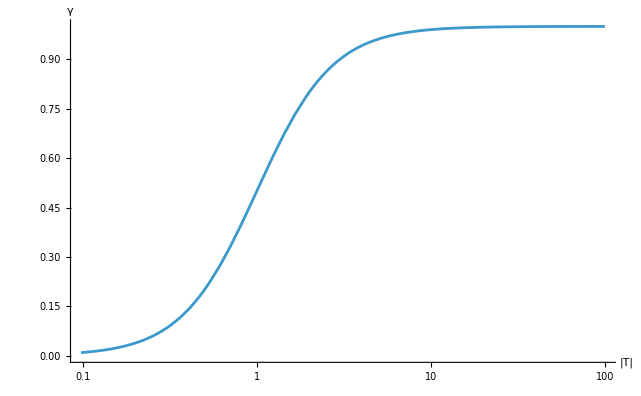

```mathematica
LogLinearPlot[γ,{T,0,100},
AxesLabel->{"|T|","γ"},PlotRange->{0,1}]
```

```mathematica
(*And to renormalize P2, divide by 1+|T|^2*)
P2av/(1+T^2)
```

P

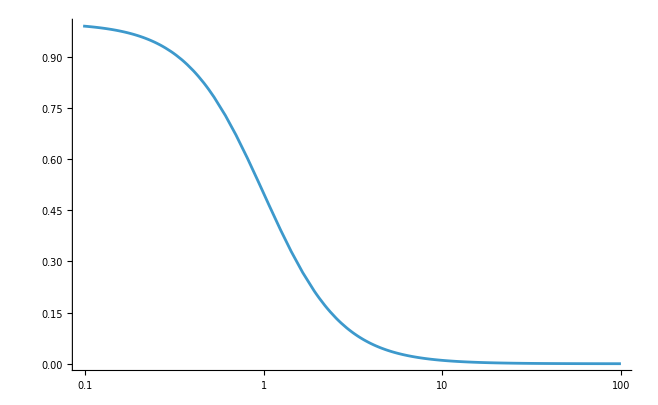

```mathematica
LogLinearPlot[1/(1+T^2),{T,0,100}]
```

```mathematica
Abs[CC]^2/(P1*P2)//ComplexExpand//FullSimplify
```

1

```mathematica
CC
```

1/2 (A-ⅈ B) P (H+ⅈ J+(A+ⅈ B) ⅇ^(ⅈ ϕ) T)

```mathematica
P1
```

1/2 (A^2+B^2) P

```mathematica
P2/.{ϕ->π/2}
```

1/2 P (H^2+J^2+2 (-B H+A J) T+(A^2+B^2) T^2)